```mathematica
Clear["Global`*"];
```

## Input Data

### Time

```mathematica
T=2.5;
Δt=0.00001;Marching=Round[T/Δt];
```

### Elements

```mathematica
ne=30;(*number of elements*)
nn=22;(*number of nodes*)
odf=62;(*open degree of freedoms*)
 L=1;
```

### Geometry

```mathematica
LL[x1_,y1_,x2_,y2_]:=√((x2-x1)^2+(y2-y1)^2);
θ[x1_,y1_,x2_,y2_]:=If[x2-x1==0,π/2,ArcTan[(y2-y1)/(x2-x1)]];
node={{0,0},{0,1},{0,2},{0,3},{0,4},{0,5},{0,6},{0,7},{0,8},{0,9},{0,10},{1,10},{1,9},{1,8},{1,7},{1,6},{1,5},{1,4},{1,3},{1,2},{1,1},{1,0}};
elmn={{1,2},{2,3},{3,4},{4,5},{5,6},{6,7},{7,8},{8,9},{9,10},{10,11},{11,12},{12,13},{13,14},{14,15},{15,16},{16,17},{17,18},{18,19},{19,20},{20,21},{21,22},{10,13},{9,14},{8,15},{7,16},{6,17},{5,18},{4,19},{3,20},{2,21}};
x1=y1=x2=y2={};
```

```mathematica
Do[
x1=Append[x1,node_⟦elmn_⟦i,1⟧,1⟧];
y1=Append[y1,node_⟦elmn_⟦i,1⟧,2⟧];
x2=Append[x2,node_⟦elmn_⟦i,2⟧,1⟧];
y2=Append[y2,node_⟦elmn_⟦i,2⟧,2⟧],{i,1,ne}];
```

```mathematica
Le=Table[LL[x1_⟦i⟧,y1_⟦i⟧,x2_⟦i⟧,y2_⟦i⟧],{i,1,ne}];
```

```mathematica
θe={Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,Pi/2,0.,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,-Pi/2,0,0,0,0,0,0,0,0,0};
```

### Material And Section Properties

```mathematica
Eee=4700000000*30^0.5;(*(Kg.f)/m^2*)
ρρ=2400;(*kg/m^3*)
A1=0.04;(*m^2 20*20*)
Ii1=1/7500;(*m^4 20*20*)
A2=0.04;(*m^2 20*20*)
Ii2=1/7500;(*m^4 20*20*)
L1=3;(*m*)
L2=3;(*m*)
cdb=0.00;
cda=0.00;
Ii=Table[Ii1,{i,ne}];A=Table[A1,{i,ne}];LLL=Table[L1,{i,ne}];
```

## Time Weight Function

```mathematica
Ca1=Table[√(Eee/(ρρ L1^2)),{i,ne}];Cb1=Table[√((Eee Ii1)/(ρρ A1 L1^4)),{i,ne}];
T1=Ca1* T;
T2=Cb1* T;
Δt1=Ca1* Δt;
Δt2=Cb1 *Δt;

m11a=Table[Δt1[[1]]^4/8,{i,ne}];m22a=Table[Δt1[[1]]^3/3,{i,ne}];m33a=Table[Δt1[[1]]^2/2,{i,ne}];

m11b=Table[Δt2[[1]]^4/8,{i,ne}];m22b=Table[Δt2[[1]]^3/3,{i,ne}];m33b=Table[Δt2[[1]]^2/2,{i,ne}];
```

## Source Function

```mathematica
Period=2.1;ϵ=0.1;
g1[x_]:=If[Δt-0.5≤x,0,If[-0.6≤x,-(x+(0.5-Δt))/Δt,If[-0.7≤x,-(-0.7+(0.5-Δt))/Δt+(x+(0.5-Δt))/Δt,0]]];g2[x_]:=If[x≤0.5-Δt,0,If[x≤0.6,(x-(0.5-Δt))/Δt,If[x≤0.7,(0.7-(0.5-Δt))/Δt-(x-(0.5-Δt))/Δt,0]]];
g2[x_]:=g1[-x];
```

```mathematica
gg1[x_]:=If[0≤Abs[x]≤ϵ,-5Abs[x]+5ϵ,0];
```

```mathematica
Needs["FourierSeries`"]
SSa=13;SSb=27;
η1=L/2+0.16;
η2=L/2+0.16;
AAλ1a=AAλ2a=Table[{},{i,1,ne}];αααa=βββ1a=βββ2a=Table[{},{i,1,ne}];ba1a=ba2a=Table[{},{i,1,ne}];
Do[
Do[
AAλ1a_⟦k⟧=Append[AAλ1a_⟦k⟧,NFourierCoefficient[g1[x],x,i,FourierParameters->{1,(-2π)/Period}]];
AAλ2a_⟦k⟧=Append[AAλ2a_⟦k⟧,NFourierCoefficient[g2[x],x,i,FourierParameters->{1,(-2π)/Period}]];
αααa_⟦k⟧=Append[αααa_⟦k⟧,(-2π i ⅈ)/Period];
βββ1a_⟦k⟧=Append[βββ1a_⟦k⟧,1/Le_⟦k⟧×(-2π i ⅈ)/Period];
βββ2a_⟦k⟧=Append[βββ2a_⟦k⟧,1/Le_⟦k⟧×(2π i ⅈ)/Period];,{i,-SSa,SSa,1}];,{k,1,ne}];
```

```mathematica
AAλ1b=Table[{},{i,1,ne}];αααb=αα=zarib=Table[{},{i,1,ne}];
Do[
Do[
AAλ1b_⟦k⟧=Append[AAλ1b_⟦k⟧,Limit[Sin[π Abs[fg]/SSb]/(π Abs[fg]/SSb), fg -> i ]NFourierSinCoefficient[gg1[x-Period/2],x,i,FourierParameters->{1,-π/Period}]];
αα_⟦k⟧=Append[αα_⟦k⟧,(π i)/Period];,{i,1,SSb,1}];,{k,1,ne}];
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0500003849284287843971878106616186371313759195800230372697114945}. NIntegrate obtained -1.37101×10^-17 and 2.08598×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.0500003849284287843971878106616186371313759195800230372697114945}. NIntegrate obtained 2.68708×10^-17 and 3.87737×10^-18 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.95000038492842869558617504378633319972458082247612765058875083923}. NIntegrate obtained -1.80217×10^-17 and 5.14552×10^-18 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Do[
Do[
αααb_⟦k⟧=Append[αααb_⟦k⟧,-αα_⟦k,i⟧ⅈ];
zarib_⟦k⟧=Append[zarib_⟦k⟧,-AAλ1b_⟦k,i⟧/(2ⅈ)];,{i,1,Length[αα_⟦k⟧]}];,{k,1,ne}];
Do[
Do[
αααb_⟦k⟧=Append[αααb_⟦k⟧,αα_⟦k,i⟧ⅈ];
zarib_⟦k⟧=Append[zarib_⟦k⟧,AAλ1b_⟦k,i⟧/(2ⅈ)];,{i,1,Length[αα_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
p1a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t^2/2+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1-(1/2(-cda+√(cda^2+4 α^2))) t)/((1/2(-cda+√(cda^2+4 α^2)))^2)];
p2a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t^2/2+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1-(1/2(-cda+√(cda^2+4 α^2))) t)/((1/2(-cda+√(cda^2+4 α^2)))^2)];
m1a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1)/(1/2(-cda+√(cda^2+4 α^2)))];
m2a[k_,α_,t_]:=If[α==0,0,(-α^2(m22a[[k]](1/2(-cda+√(cda^2+4 α^2)))+m33a[[k]])+cda (1/2(-cda+√(cda^2+4 α^2))) m33a[[k]])/(((1/2(-cda+√(cda^2+4 α^2))))^2(-α^2 m11a[[k]]+cda m22a[[k]]+m33a[[k]]))t+(ⅇ^((1/2(-cda+√(cda^2+4 α^2))) t)-1)/(1/2(-cda+√(cda^2+4 α^2)))];,{k,1,ne}];
```

```mathematica
Do[
p1b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-cdb+√(cdb^2-4 α^4))) m22b[[k]])+cdb (1/2(-cdb+√(cdb^2-4 α^4))) m33b[[k]])/((1/2(-cdb+√(cdb^2-4 α^4)))^2(α^4 m11b[[k]]+cdb m22b[[k]]+m33b[[k]])) t^2/2+(ⅇ^((1/2(-cdb+√(cdb^2-4 α^4))) t)- (1/2(-cdb+√(cdb^2-4 α^4))) t-1)/((1/2(-cdb+√(cdb^2-4 α^4)))^2)];
p2b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-cdb+√(cdb^2-4 α^4))) m22b[[k]])+cdb (1/2(-cdb+√(cdb^2-4 α^4))) m33b[[k]])/((1/2(-cdb+√(cdb^2-4 α^4)))^2(α^4 m11b[[k]]+cdb m22b[[k]]+m33b[[k]])) t^2/2+(ⅇ^((1/2(-cdb+√(cdb^2-4 α^4))) t)- (1/2(-cdb+√(cdb^2-4 α^4))) t-1)/((1/2(-cdb+√(cdb^2-4 α^4)))^2)];

m1b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-cdb+√(cdb^2-4 α^4))) m22b[[k]])+cdb (1/2(-cdb+√(cdb^2-4 α^4))) m33b[[k]])/((1/2(-cdb+√(cdb^2-4 α^4)))^2(α^4 m11b[[k]]+cdb m22b[[k]]+m33b[[k]])) t+(ⅇ^((1/2(-cdb+√(cdb^2-4 α^4))) t)-1)/(1/2(-cdb+√(cdb^2-4 α^4)))];
m2b[k_,α_,t_]:=If[α==0,0,(α^4(m33b[[k]]+(1/2(-cdb+√(cdb^2-4 α^4))) m22b[[k]])+cdb (1/2(-cdb+√(cdb^2-4 α^4))) m33b[[k]])/((1/2(-cdb+√(cdb^2-4 α^4)))^2(α^4 m11b[[k]]+cdb m22b[[k]]+m33b[[k]])) t+(ⅇ^((1/2(-cdb+√(cdb^2-4 α^4))) t)-1)/(1/2(-cdb+√(cdb^2-4 α^4)))];,{k,1,ne}];
```

```mathematica
Do[
Do[
If[
αααa_⟦k,i⟧≠0,
AAλ1a_⟦k,i⟧=AAλ1a_⟦k,i⟧/p1a[k,αααa_⟦k,i⟧,Δt1[[k]]];
AAλ2a_⟦k,i⟧=AAλ2a_⟦k,i⟧/p2a[k,αααa_⟦k,i⟧,Δt1[[k]]];,
ba1a_⟦k⟧=AAλ1a_⟦k,i⟧;ba2a_⟦k⟧=AAλ2a_⟦k,i⟧;];
,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
zarib1=zarib2=zarib3=zarib4=zarib;ba1b=ba2b=ba3b=ba4b=Table[{},{i,1,ne}];

Do[
Do[
zarib1_⟦k,i⟧=zarib_⟦k,i⟧/p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] ⅇ^(αααb_⟦k,i⟧ (-Period/2+η1));
zarib2_⟦k,i⟧=zarib_⟦k,i⟧/(-αααb_⟦k,i⟧p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb_⟦k,i⟧ (-Period/2+η2));
zarib3_⟦k,i⟧=zarib_⟦k,i⟧/p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] ⅇ^(αααb_⟦k,i⟧ (-Period/2-η1));
zarib4_⟦k,i⟧=zarib_⟦k,i⟧/(αααb_⟦k,i⟧p2b[k,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb_⟦k,i⟧ (-Period/2-η2));,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
h0a=l0a=Table[{},{i,1,ne}];
Do[
h0a_⟦k⟧=ba1a_⟦k⟧/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);l0a_⟦k⟧=ba2a_⟦k⟧/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);

I1a[k_,x_]:=∑_(i=1)^Length[αααa_⟦k⟧] (ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])+h0a_⟦k⟧ (-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);
I2a[k_,x_]:=∑_(i=1)^Length[αααa_⟦k⟧] (ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]])+l0a_⟦k⟧ (-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);,{k,1,ne}];
```

```mathematica
Do[
dis2[k_]=-∑_(i=1)^Length[αααb_⟦k⟧] (p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧);
dis4[k_]=-∑_(i=1)^Length[αααb_⟦k⟧] (p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧);

I1b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧);
I1bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I1bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I1bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib1_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);I2b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧)+dis2[k];
I2bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I2bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I2bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib2_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);
I3b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧);
I3bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I3bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I3bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib3_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);
I4b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧)+dis4[k];
I4bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧αααb_⟦k,i⟧/LLL[[k]]);
I4bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^2);I4bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ⅇ^(αααb_⟦k,i⟧×x)p2b[k,αααb_⟦k,i⟧,Δt2[[k]]] zarib4_⟦k,i⟧(αααb_⟦k,i⟧/LLL[[k]])^3);,{k,1,ne}];
```

## Shape Functions

```mathematica
z1=Inverse[({{I1b[1,-L/2], I2b[1,-L/2], I3b[1,-L/2], I4b[1,-L/2]}, {I1bα[1,-L/2], I2bα[1,-L/2], I3bα[1,-L/2], I4bα[1,-L/2]}, {I1b[1,L/2], I2b[1,L/2], I3b[1,L/2], I4b[1,L/2]}, {I1bα[1,L/2], I2bα[1,L/2], I3bα[1,L/2], I4bα[1,L/2]}})].({{1}, {0}, {0}, {0}});z2=Inverse[({{I1b[1,-L/2], I2b[1,-L/2], I3b[1,-L/2], I4b[1,-L/2]}, {I1bα[1,-L/2], I2bα[1,-L/2], I3bα[1,-L/2], I4bα[1,-L/2]}, {I1b[1,L/2], I2b[1,L/2], I3b[1,L/2], I4b[1,L/2]}, {I1bα[1,L/2], I2bα[1,L/2], I3bα[1,L/2], I4bα[1,L/2]}})].({{0}, {1}, {0}, {0}});z3=Inverse[({{I1b[1,-L/2], I2b[1,-L/2], I3b[1,-L/2], I4b[1,-L/2]}, {I1bα[1,-L/2], I2bα[1,-L/2], I3bα[1,-L/2], I4bα[1,-L/2]}, {I1b[1,L/2], I2b[1,L/2], I3b[1,L/2], I4b[1,L/2]}, {I1bα[1,L/2], I2bα[1,L/2], I3bα[1,L/2], I4bα[1,L/2]}})].({{0}, {0}, {1}, {0}});z4=Inverse[({{I1b[1,-L/2], I2b[1,-L/2], I3b[1,-L/2], I4b[1,-L/2]}, {I1bα[1,-L/2], I2bα[1,-L/2], I3bα[1,-L/2], I4bα[1,-L/2]}, {I1b[1,L/2], I2b[1,L/2], I3b[1,L/2], I4b[1,L/2]}, {I1bα[1,L/2], I2bα[1,L/2], I3bα[1,L/2], I4bα[1,L/2]}})].({{0}, {0}, {0}, {1}});
```

```mathematica
ZZ1=ZZ2=ZZ3=ZZ4={};
```

```mathematica
Do[
ZZ1=Append[ZZ1,(z1[[1,1]]*zarib1_⟦1,i⟧+z1[[2,1]] zarib2_⟦1,i⟧+z1[[3,1]] zarib3_⟦1,i⟧+z1[[4,1]] zarib4_⟦1,i⟧)];
ZZ2=Append[ZZ2,(z2[[1,1]]*zarib1_⟦1,i⟧+z2[[2,1]] zarib2_⟦1,i⟧+z2[[3,1]] zarib3_⟦1,i⟧+z2[[4,1]] zarib4_⟦1,i⟧)];
ZZ3=Append[ZZ3,(z3[[1,1]]*zarib1_⟦1,i⟧+z3[[2,1]] zarib2_⟦1,i⟧+z3[[3,1]] zarib3_⟦1,i⟧+z3[[4,1]] zarib4_⟦1,i⟧)];
ZZ4=Append[ZZ4,(z4[[1,1]]*zarib1_⟦1,i⟧+z4[[2,1]] zarib2_⟦1,i⟧+z4[[3,1]] zarib3_⟦1,i⟧+z4[[4,1]] zarib4_⟦1,i⟧)];
,{i,1,Length[αααb[[1]]]}];
```

```mathematica
con1=z1[[1,1]]*0+z1[[2,1]]dis2[1]+z1[[3,1]]*0+z1[[4,1]]dis4[1];
con2=z2[[1,1]]*0+z2[[2,1]]dis2[1]+z2[[3,1]]*0+z2[[4,1]]dis4[1];
con3=z3[[1,1]]*0+z3[[2,1]]dis2[1]+z3[[3,1]]*0+z3[[4,1]]dis4[1];
con4=z4[[1,1]]*0+z4[[2,1]]dis2[1]+z4[[3,1]]*0+z4[[4,1]]dis4[1];

N1b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con1;
N1bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N1bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N1bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ1[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;

N2b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con2;
N2bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N2bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N2bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ2[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;


N3b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con3;
N3bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N3bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N3bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ3[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;

N4b[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))+con4;
N4bα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]]);

N4bαα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^2;

N4bααα[k_,x_]:=∑_(i=1)^Length[αααb_⟦k⟧] (ZZ4[[i]](p2b[1,αααb_⟦k,i⟧,Δt2[[k]]])ⅇ^(αααb[[k,i]]x))(αααb_⟦k,i⟧/LLL[[k]])^3;
```

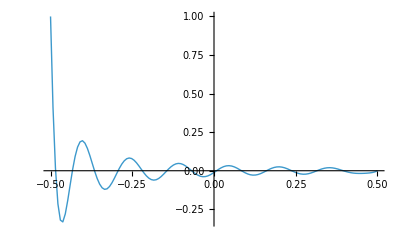

```mathematica
Plot[{Re[N2bα[1,x]]},{x,-0.5,0.5},PlotPoints->3,PlotRange->All,PlotStyle->Thick]
```

```mathematica
S1a=S2a=Table[{},{i,1,ne}];
Do[
S1a_⟦k⟧=I1a[k,-L/2];S2a_⟦k⟧=I1a[k,L/2];
N1a[k_,x_]:=S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)I1a[k,x]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I2a[k,x];
N2a[k_,x_]:=-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I1a[k,x]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) I2a[k,x];,{k,1,ne}];
```

```mathematica
Do[
N1αa[k_,x_]:=(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]));
N2αa[k_,x_]:=(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]])+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2) ∑_(i=1)^Length[αααa_⟦k⟧] (αααa_⟦k,i⟧×ⅇ^(αααa_⟦k,i⟧×x)×AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]));,{k,1,ne}];
```

## Stiffness Matrix

```mathematica
k1[Le_,θ_,el_]:=Transpose[({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})].({{-(Eee×A[[el]])/LLL[[el]]N1αa[el,-L/2], 0, 0}, {0, Eee×Ii[[el]]×N1bααα[el,-L/2], Eee×Ii[[el]]×N2bααα[el,-L/2]}, {0, -Eee×Ii[[el]]×N1bαα[el,-L/2], -Eee×Ii[[el]]×N2bαα[el,-L/2]}}).({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
k2[Le_,θ_,el_]:=Transpose[({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})].({{(Eee×A[[el]])/LLL[[el]]×N2αa[el,L/2], 0, 0}, {0, -Eee×Ii[[el]]×N3bααα[el,L/2], -Eee×Ii[[el]]×N4bααα[el,L/2]}, {0, Eee×Ii[[el]]×N3bαα[el,L/2], Eee×Ii[[el]]×N4bαα[el,L/2]}}).({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
```

```mathematica
ke1=ke2={};
Do[AppendTo[ke1,k1[Le_⟦i⟧,θe_⟦i⟧,i]];
AppendTo[ke2,k2[Le_⟦i⟧,θe_⟦i⟧,i]];
,{i,1,ne}];
```

```mathematica
Table[MatrixForm[ke1_⟦i⟧],{i,ne}];Table[MatrixForm[ke2_⟦i⟧],{i,ne}];
MatrixForm[ke1];
```

```mathematica
t[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}});
B1=({{1, 2}, {2, 3}, {3, 4}, {4, 5}, {5, 6}, {6, 7}, {7, 8}, {8, 9}, {9, 10}, {10, 11}, {11, 12}, {12, 13}, {13, 14}, {14, 15}, {15, 16}, {16, 17}, {17, 18}, {18, 19}, {19, 20}, {20, 21}, {21, 22}, {10, 13}, {9, 14}, {8, 15}, {7, 16}, {6, 17}, {5, 18}, {4, 19}, {3, 20}, {2, 21}});
te={};
Do[AppendTo[te,t[θe_⟦i⟧]],{i,1,ne}];
Table[MatrixForm[te_⟦i⟧],{i,ne}];
MatrixForm[te[[1]]];
```

```mathematica
K=Table[0,{i,nn},{j,3},{r,3}];
For[i=1,i≤ne,i++,
For[j=1,j≤2,j++,
If[j==1,K_⟦B1_⟦i,j⟧⟧+=ke1_⟦i⟧,K_⟦B1_⟦i,j⟧⟧+=ke2_⟦i⟧];
];
];
```

### Open degree of freedom

```mathematica
odf1=ReplacePart[Table[3,{i,nn}],{1->1,22->1}];
dof=Table[0,{i,nn},{j,3}];
dof=ReplacePart[dof,{{1,2}->1,{1,3}->1,{22,2}->1,{22,3}->1}];
```

### Assembling

```mathematica
K1=Kuu={};

Do[
K1=Append[K1,Table[0,{j,odf1[[i]]},{r,3}]];
Kuu=Append[Kuu,Table[0,{j,odf1[[i]]},{r,odf1[[i]]}]];
,{i,1,nn}]
```

```mathematica
For[i=1,i≤nn,i++,
For[j=1,j≤odf1[[i]],j++,
K1_⟦i,j,All⟧=K_⟦i,Ordering[dof[[i]]]_⟦j⟧,All⟧
];
];
For[i=1,i≤nn,i++,
For[j=1,j≤odf1[[i]],j++,
Kuu_⟦i,All,j⟧=K1_⟦i,All,Ordering[dof[[i]]]_⟦j⟧⟧
];
];
```

```mathematica
FF={};
Do[
FF=Append[FF,If[Length[Kuu[[i]]]==0,0,Inverse[Kuu[[i]]]]];
,{i,1,nn}];
```

## Force And Initial Displacement

```mathematica
AAa=Table[{},{i,1,ne}];
Do[Do[AAa_⟦k⟧=Append[AAa_⟦k⟧,0],{j,1,Length[αααa_⟦k⟧]}],{k,1,ne}];
AAb=Table[{},{i,1,ne}];
Do[Do[AAb_⟦k⟧=Append[AAb_⟦k⟧,0],{j,1,Length[αααb_⟦k⟧]}],{k,1,ne}];
BBa=Table[{},{i,1,ne}];
Do[Do[BBa_⟦k⟧=Append[BBa_⟦k⟧,0],{j,1,Length[αααa_⟦k⟧]}],{k,1,ne}];
BBb=Table[{},{i,1,ne}];
Do[Do[BBb_⟦k⟧=Append[BBb_⟦k⟧,0],{j,1,Length[αααb_⟦k⟧]}],{k,1,ne}];
```

```mathematica
disa=Table[{},{i,1,ne}];
Do[disa_⟦k⟧=0,{k,1,ne}];

dis22a=Table[{},{i,1,ne}];
Do[dis22a_⟦k⟧=0,{k,1,ne}];

disb=Table[{},{i,1,ne}];
Do[disb_⟦k⟧=0,{k,1,ne}];

dis22b=Table[{},{i,1,ne}];
Do[dis22b_⟦k⟧=0,{k,1,ne}];(*exponential base coefficients*)
```

```mathematica
RR1=Table[0,{i,ne},{k,3},{h,1}];RR2=Table[0,{i,ne},{k,3},{h,1}];R1=Table[0,{j,6 nn},{k,1}];Ru=Table[0,{j,odf},{k,1}];Ru1=Table[0,{j,odf-2},{k,1}];ww=Table[0,{j,nn},{k,3}];wwt=Table[0,{j,6 nn},{k,1}];wwe=Table[0,{i,ne},{k,6},{h,1}];wwe1=Table[0,{i,ne},{k,3},{h,1}];wwe2=Table[0,{i,ne},{k,3},{h,1}];Δwe6=Table[0,{i,ne},{k,6},{h,1}];Δwe61=Table[0,{i,ne},{k,3},{h,1}];Δwe62=Table[0,{i,ne},{k,3},{h,1}];CC=Table[0,{i,ne},{k,4},{h,1}];wa=wb=wc=Table[0,{i,Marching}];
```

```mathematica
BPc={-L/2,L/2};
BPa=Table[0,{k,1,ne},{q,1,2},{i,1,Length[αααa_⟦1⟧]}];
BPb=Table[0,{k,1,ne},{q,1,2},{i,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Do[
BPa_⟦k,q,i⟧=ⅇ^(αααa_⟦k,i⟧×BPc_⟦q⟧);,{i,1,Length[αααa_⟦k⟧]}];,{q,1,2}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Do[
BPb_⟦k,q,i⟧=ⅇ^(αααb_⟦k,i⟧×BPc_⟦q⟧);,{i,1,Length[αααb_⟦k⟧]}];,{q,1,2}];,{k,1,ne}];
```

```mathematica
Ezafea=Table[{},{k,1,ne},{i,1,Length[αααa_⟦1⟧]}];
Ezafeb=Table[{},{k,1,ne},{i,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Ezafea_⟦k,i⟧=Append[Ezafea_⟦k,i⟧,m33a[[k]]/(αααa_⟦k,i⟧^2 m11a[[k]]-cda m22a[[k]]-m33a[[k]])Δt1[[k]]^2/2];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Ezafeb_⟦k,i⟧=Append[Ezafeb_⟦k,i⟧,(αααb_⟦k,i⟧^4  m33b[[k]])/(αααb_⟦k,i⟧^4*m11b[[k]]+cdb m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Source1a=Source2a=Table[{},{i,1,ne},{j,1,Length[αααa_⟦1⟧]}];
Source1b=Source2b=Source3b=Source4b=Table[{},{i,1,ne},{j,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Source1a_⟦k,i⟧=Append[Source1a_⟦k,i⟧,S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];
Source2a_⟦k,i⟧=Append[Source2a_⟦k,i⟧,-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×p1a[k,αααa_⟦k,i⟧,Δt1[[k]]]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×p2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Source1b_⟦k,i⟧=Append[Source1b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ1[[i]]];
Source2b_⟦k,i⟧=Append[Source2b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ2[[i]]];
Source3b_⟦k,i⟧=Append[Source3b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ3[[i]]];
Source4b_⟦k,i⟧=Append[Source4b_⟦k,i⟧,p2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ4[[i]]];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Sourcett1a=Sourcett2a=Table[{},{i,1,ne},{j,1,Length[αααa_⟦1⟧]}];
Sourcett1b=Sourcett2b=Sourcett3b=Sourcett4b=Table[{},{i,1,ne},{j,1,Length[αααb_⟦1⟧]}];
```

```mathematica
Do[
Do[
Sourcett1a_⟦k,i⟧=Append[Sourcett1a_⟦k,i⟧,S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×m1a[k,αααa_⟦k,i⟧,Δt1[[k]]]-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×m2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];
Sourcett2a_⟦k,i⟧=Append[Sourcett2a_⟦k,i⟧,-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ1a_⟦k,i⟧×m1a[k,αααa_⟦k,i⟧,Δt1[[k]]]+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)AAλ2a_⟦k,i⟧×m2a[k,αααa_⟦k,i⟧,Δt1[[k]]]];,{i,1,Length[αααa_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
Do[
Do[
Sourcett1b_⟦k,i⟧=Append[Sourcett1b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ1_⟦i⟧];
Sourcett2b_⟦k,i⟧=Append[Sourcett2b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ2_⟦i⟧];
Sourcett3b_⟦k,i⟧=Append[Sourcett3b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ3_⟦i⟧];
Sourcett4b_⟦k,i⟧=Append[Sourcett4b_⟦k,i⟧,m2b[k,αααb_⟦k,i⟧,Δt2[[k]]]×ZZ4_⟦i⟧];,{i,1,Length[αααb_⟦k⟧]}];,{k,1,ne}];
```

```mathematica
rr=0;
 aa=ab=Table[0,{i,ne}];
```

```mathematica
Do[
aa[[k]]=(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]+Δt1[[k]]^2/2)/(-(cda m11a[[k]]+m22a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2+Δt1[[k]]^3/6);
ab[[k]]=(-(cdb m11b[[k]]+m22b[[k]])/(cdb m22b[[k]]+m33b[[k]])Δt2[[k]]^1/1+Δt2[[k]]^2/2)/(-(cdb m11b[[k]]+m22b[[k]])/(cdb m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2+Δt2[[k]]^3/6);,{k,1,ne}];
```

```mathematica
www={};
Do[
www=Append[www,Table[0,{r,odf1[[i]]}]];
,{i,1,nn}];
```

## Main Program

```mathematica
Do[
COa=AAa(1-Ezafea αααa^2)+BBa(Δt1-Ezafea×((αααa^2 m22a)/m33a-cda));
COαa=αααa×COa;
COb=AAb(1-Ezafeb)+BBb(Δt2-Ezafeb×((m22b)/m33b+cdb/αααb^4));
COαb=αααb×COb;
COααb=(αααb)^2×COb;
COαααb=(αααb)^3×COb;


f=fα=Table[{},{i,1,6}];
f1=fα1=Table[{},{i,1,3}];f2=fα2=Table[{},{i,1,3}];


Do[
f1_⟦1⟧=Append[f1_⟦1⟧,Flatten[COa_⟦k⟧].Transpose[BPa_⟦k,1,All⟧,{1}]+dis22a_⟦k⟧(Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2)+disa_⟦k⟧];
f1_⟦2⟧=Append[f1_⟦2⟧,Flatten[COb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]+dis22b_⟦k⟧ Δt2[[k]]+disb_⟦k⟧-(cdb m33b[[k]] dis22b_⟦k⟧)/(cdb m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];
f1_⟦3⟧=Append[f1_⟦3⟧,1/LLL[[k]]*Flatten[COαb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];


f2_⟦1⟧=Append[f2_⟦1⟧,Flatten[COa_⟦k⟧].Transpose[BPa_⟦k,2,All⟧,{1}]+dis22a_⟦k⟧ (Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]]^2/2)+disa_⟦k⟧];
f2_⟦2⟧=Append[f2_⟦2⟧,Flatten[COb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]+dis22b_⟦k⟧ Δt2[[k]]+disb_⟦k⟧-(cdb m33b[[k]] dis22b_⟦k⟧)/(cdb m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2];
f2_⟦3⟧=Append[f2_⟦3⟧,1/LLL[[k]]*Flatten[COαb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];

,{k,1,ne}];

Do[
fα1_⟦1⟧=Append[fα1_⟦1⟧,-(Eee×A[[k]])/LLL[[k]]×Flatten[COαa_⟦k⟧].Transpose[BPa_⟦k,1,All⟧,{1}]];
fα1_⟦2⟧=Append[fα1_⟦2⟧,(Eee×Ii[[k]])/LLL[[k]]^3×Flatten[COαααb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];
fα1_⟦3⟧=Append[fα1_⟦3⟧,-(Eee×Ii[[k]])/LLL[[k]]^2×Flatten[COααb_⟦k⟧].Transpose[BPb_⟦k,1,All⟧,{1}]];

fα2_⟦1⟧=Append[fα2_⟦1⟧,(Eee×A[[k]])/LLL[[k]]×Flatten[COαa_⟦k⟧].Transpose[BPa_⟦k,2,All⟧,{1}]];
fα2_⟦2⟧=Append[fα2_⟦2⟧,-(Eee×Ii[[k]])/LLL[[k]]^3×Flatten[COαααb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];
fα2_⟦3⟧=Append[fα2_⟦3⟧,(Eee×Ii[[k]])/LLL[[k]]^2×Flatten[COααb_⟦k⟧].Transpose[BPb_⟦k,2,All⟧,{1}]];
,{k,1,ne}];(*Subscript[f, i]^n*)

Do[
RR1_⟦k⟧=(ke1_⟦k⟧.(Transpose[te_⟦k⟧].f1_⟦All,k⟧))-(Transpose[te_⟦k⟧].fα1_⟦All,k⟧);
RR2_⟦k⟧=(ke2_⟦k⟧.(Transpose[te_⟦k⟧].f2_⟦All,k⟧))-(Transpose[te_⟦k⟧].fα2_⟦All,k⟧);
,{k,1,ne}];
RR=Table[0,{i,nn},{k,3},{h,1}];
For[i=1,i≤ne,i++,
For[r=1,r≤2,r++,
If[r==1,RR_⟦B1_⟦i,r⟧⟧+=RR1_⟦i⟧,RR_⟦B1_⟦i,r⟧⟧+=RR2_⟦i⟧];
];
];


Ru={};
Do[
Ru=Append[Ru,Table[0,{r,odf1[[i]]}]];
,{i,1,nn}];


For[i=1,i≤nn,i++,
For[r=1,r≤odf1[[i]],r++,
Ru_⟦i,r⟧=RR_⟦i,Ordering[dof[[i]]]_⟦r⟧⟧
];
];



Do[
If[Length[FF[[i]]]≠0,www[[i]]=FF[[i]].(Ru[[i]])];
,{i,2,nn-1}];(*u^- and w^-*)

www[[1]]={{25/(5 Pi)^2-25 Cos[5 Pi Δt j]/(5 Pi)^2}};
www[[22]]={{37.5/(5 Pi)^2-37.5 Cos[5 Pi Δt j]/(5 Pi)^2}};

For[i=1,i≤nn,i++,
For[r=1,r≤3,r++,
If[dof_⟦i,r⟧≠1,ww_⟦i,r⟧=Flatten[www_⟦i,r⟧][[1]];
];
];
];

For[ele=1,ele≤ne,ele++,
For[r=1,r≤3,r++,
wwe1_⟦ele,r⟧=ww_⟦B1_⟦ele,1⟧,r⟧;
wwe2_⟦ele,r⟧=ww_⟦B1_⟦ele,2⟧,r⟧;
];
];


Do[
Δwe61_⟦i⟧=te_⟦i⟧.(Flatten[(wwe1_⟦i⟧)-(Transpose[te_⟦i⟧].f1_⟦All,i⟧)]);
Δwe62_⟦i⟧=te_⟦i⟧.(Flatten[(wwe2_⟦i⟧)-(Transpose[te_⟦i⟧].f2_⟦All,i⟧)]);
,{i,1,ne}];

wa[[j]]=Re[ww[[6,1]]];wb[[j]]=Re[ww[[6,2]]];wc[[j]]=Re[ww[[6,3]]];

If[j≠Marching,
BBa=BBa×(1-Ezafea ((αααa^2 m22a)/m33a -cda)2/Δt1)-AAa×Ezafea αααa^2×2/Δt1+Sourcett1a×Δwe61_⟦;;,1⟧+Sourcett2a×Δwe62_⟦;;,1⟧;


BBb=BBb×(1-Ezafeb(m22b/m33b+cdb/αααb^4)2/Δt2)-AAb×Ezafeb×2/Δt2+
Sourcett1b×Δwe61_⟦;;,2⟧+Sourcett2b×Δwe61_⟦;;,3⟧+Sourcett3b×Δwe62_⟦;;,2⟧+Sourcett4b×Δwe62_⟦;;,3⟧;


AAa=COa+Source1a×Δwe61_⟦;;,1⟧+Source2a×Δwe62_⟦;;,1⟧;

AAb=COb+Source1b×Δwe61_⟦;;,2⟧+Source2b×Δwe61_⟦;;,3⟧+Source3b×Δwe62_⟦;;,2⟧+Source4b×Δwe62_⟦;;,3⟧;

Do[
disa_⟦k⟧=disa_⟦k⟧+dis22a_⟦k⟧ (Δt1[[k]]-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]]) Δt1[[k]]^2/2)+(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)Δwe61_⟦k,1⟧+(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)Δwe62_⟦k,1⟧;

dis22a_⟦k⟧=dis22a_⟦k⟧ (1-(cda m33a[[k]])/(cda m22a[[k]]+m33a[[k]])Δt1[[k]])+(S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧) (aa[[k]])Δwe61_⟦k,1⟧+(-S2a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba1a_⟦k⟧+S1a_⟦k⟧/(S1a_⟦k⟧^2-S2a_⟦k⟧^2)ba2a_⟦k⟧)(aa[[k]])Δwe62_⟦k,1⟧;

disb_⟦k⟧=disb_⟦k⟧+dis22b_⟦k⟧ (Δt2[[k]]-(cdb m33b[[k]])/(cdb m22b[[k]]+m33b[[k]])Δt2[[k]]^2/2)+con1×Δwe61_⟦k,2⟧+con2×Δwe61_⟦k,3⟧+con3×Δwe62_⟦k,2⟧+con4×Δwe62_⟦k,3⟧;


dis22b_⟦k⟧=dis22b_⟦k⟧(1-(cdb m33b[[k]])/(cdb m22b[[k]]+m33b[[k]])Δt2[[k]])+(con1×Δwe61_⟦k,2⟧+con2×Δwe61_⟦k,3⟧+con3×Δwe62_⟦k,2⟧+con4×Δwe62_⟦k,3⟧)ab[[k]];
,{k,1,ne}];

];(*Update exponential base coefficients*)
,{j,1,Marching}];
```

## Result

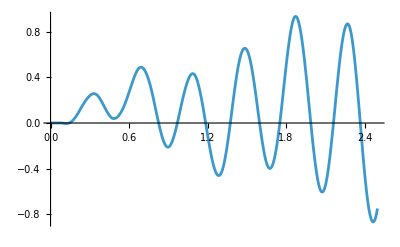

```mathematica
ListPlot[Table[{i Δt,wa[[i]]},{i,1,Marching,100}],PlotRange->All,Joined->True]
```